# Zapori v Evropki uniji

Datum : 23. 3. 2021

## Podatki, ki jih bomo uporabili:

```mathematica
drzaveEU = CountryData["EU", "Name"];
```

```mathematica
steviloZapornikovAbs = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_absolutno.xlsx"][[1]];
```

```mathematica
jeVEU[x_]:= MemberQ[drzaveEU, CountryData[x]]; (*Funkcija preveri ali je država članica EU.*)
```

```mathematica
drzaveEUZaporniki =Select[steviloZapornikovAbs,MemberQ[drzaveEU, #[[1]]]&];
```

```mathematica
zapornikiSlovenija = Select[steviloZapornikovAbs, #[[1]] == "Slovenia"&];
```

```mathematica
zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]]; (*Število zaprtih po letih v Slovenije med leti 2009 in 2018*)
```

```mathematica
zapornikiSlovenijaTS = TimeSeries[zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]], {Range[2009, 2018]}](*Časovna vrsta zaporniki Slovenija.*)
```

TimeSeries[…]

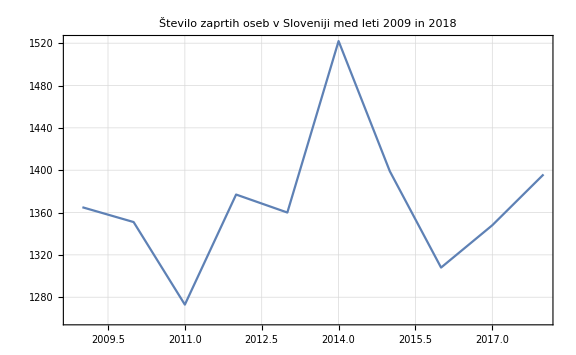

```mathematica
ListLinePlot[zapornikiSlovenijaTS, PlotLabel->Style["Število zaprtih oseb v Sloveniji med leti 2009 in 2018", 16, Darker[Blue], Background->Lighter[Yellow]], ImageSize->Large, PlotTheme->"Detailed"]
```

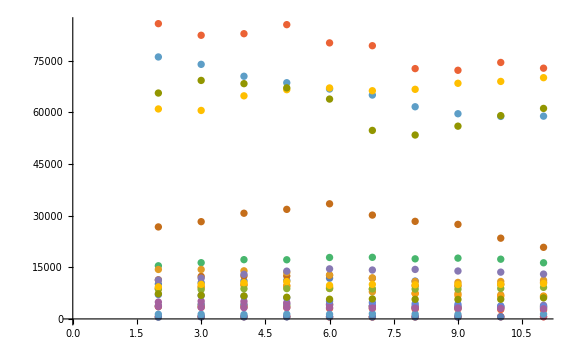

```mathematica
ListPlot[drzaveEUZaporniki, ImageSize->Large]
```

```mathematica
s = steviloZapornikovAbs[[1]];
```

```mathematica
steviloZapornikovEU1 = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx", {"Data", 5, Range[9, 51]}];
```

```mathematica
stZaprtiPoLetuEU = Select[steviloZapornikovEU, MemberQ[drzaveEU,#[[0]]]&]
```

{}

```mathematica
steviloZapornikovEU = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx"];
```

```mathematica
steviloZapornikovEU[[5]]//Grid;
```